```mathematica
G[t_] := HeavisideTheta[t+1/2] -  HeavisideTheta[t-1/2]
```

```mathematica
FourierTransform[G[t],t,ω,FourierParameters->{1, -1}]
```

(2 Sin[ω/2])/ω

```mathematica
T[t_]:=(1-Abs[t])*G[t/2]
```

```mathematica
TrigFactor[ExpToTrig[FourierTransform[T[t],t,ω,FourierParameters->{1, -1}]]]
```

(4 Sin[ω/2]^2)/ω^2

```mathematica
FullSimplify[TrigFactor[ExpToTrig[FourierTransform[T[t]+T[t-1]+T[t-2],t,ω,FourierParameters->{1, -1}]]]//.Sin[ω/2]->ω/2 q]
```

ⅇ^(-ⅈ ω) q^2 (1+2 Cos[ω])

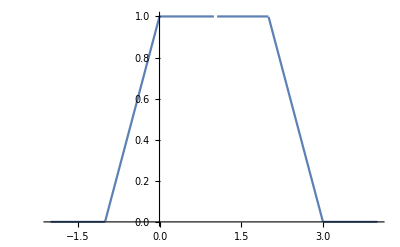

```mathematica
Plot[T[t]+T[t-1]+T[t-2],{t,-2,4}]
```

```mathematica
FullSimplify[TrigFactor[ExpToTrig[FourierTransform[-T[t]+T[t-2],t,ω,FourierParameters->{1, -1}]]]//.Sin[ω/2]->ω/2 q]
```

-2 ⅈ ⅇ^(-ⅈ ω) q^3 ω Cos[ω/2]

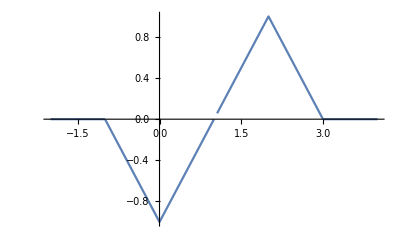

```mathematica
Plot[-T[t]+T[t-2],{t,-2,4}]
```

```mathematica
FullSimplify[TrigToExp[TrigFactor[ExpToTrig[FourierTransform[-T[t+1]-T[t]+T[t-2],t,ω,FourierParameters->{1, -1}]]]//.Sin[ω/2]^2->ω^2/4 q^2]]
```

-ⅇ^(-2 ⅈ ω) (-1+ⅇ^(2 ⅈ ω)+ⅇ^(3 ⅈ ω)) q^2

```mathematica
FourierTransform[F'[x],x,ω,FourierParameters->{1, -1}]
```

ⅈ ω FourierTransform[F[x],x,ω]

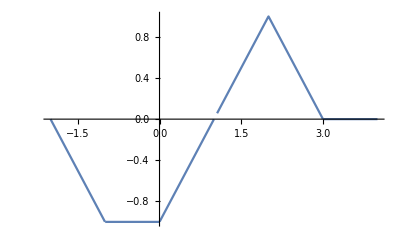

```mathematica
Plot[-T[t+1]-T[t]+T[t-2],{t,-2,4}]
```

```mathematica
TrigFactor[ExpToTrig[FourierTransform[T[x/2],x,f,FourierParameters->{0,-2π}]]]
```

(2 Cos[f π]^2 Sin[f π]^2)/(f^2 π^2)

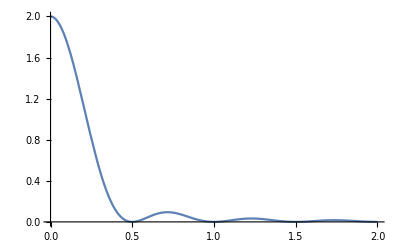

```mathematica
Plot[%,{f,0,2},PlotRange->Full]
```

```mathematica
TrigExpand[Sin[2τ]]
```

2 Cos[τ] Sin[τ]

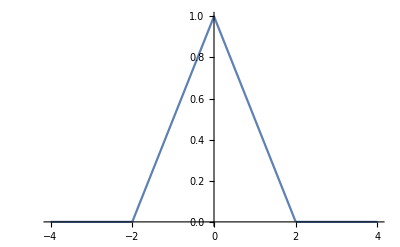

```mathematica
Plot[T[t/2],{t,-4,4}]
```

```mathematica
K[t_]:=Sum[DiscreteDelta[t-k]+DiscreteDelta[t-2k],{k,-∞,∞}]
```

```mathematica
FourierSequenceTransform[Sum[DiscreteDelta[t-k]+DiscreteDelta[t-2k],{k,-∞,∞}],t,ω,FourierParameters->{1, 1}]
```

ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))-ⅇ^(2 ⅈ ω)/(-1+ⅇ^(ⅈ ω))+2 π DiracDelta[ω]

```mathematica
Sum[K[n]Exp[-ⅈ n ω 1/L],{n,0,L-1}]//.L->2
```

(2 ⅇ^(-(ⅈ ω)/2) (-1+ⅇ^(ⅈ ω)))/(-1+ⅇ^((ⅈ ω)/2))

```mathematica
FourierTransform[Sum[DiracDelta[t-k]+DiracDelta[t-2k],{k,-∞,∞}],t,ω,FourierParameters->{1, -1}]
```

∑_(k=-∞)^∞ (Cos[k ω]+Cos[2 k ω]-ⅈ (Sin[k ω]+Sin[2 k ω]))

```mathematica
TrigToExp[Cos[k ω]+ⅈ Sin[k ω]]
```

ⅇ^(ⅈ k ω)

```mathematica
∑_(k=-∞)^∞ ⅇ^(-2 ⅈ k ω) (UnitStep[-1-2 k]+ⅇ^(ⅈ k ω) UnitStep[-1-k]+ⅇ^(ⅈ k ω) UnitStep[k]+UnitStep[2 k])
```

0

```mathematica
∑_(k=-∞)^-1 ⅇ^(-2 ⅈ k ω)
∑_(k=-∞)^-1 ⅇ^(- ⅈ k ω)
∑_(k=0)^∞ ⅇ^(-ⅈ k ω)
∑_(k=0)^∞ ⅇ^(-2 ⅈ k ω)
```

-ⅇ^(2 ⅈ ω)/(-1+ⅇ^(2 ⅈ ω))

-ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))

ⅇ^(ⅈ ω)/(-1+ⅇ^(ⅈ ω))

ⅇ^(2 ⅈ ω)/(-1+ⅇ^(2 ⅈ ω))

```mathematica
FullSimplify[(2+ⅇ^(ⅈ ω))/((-1+ⅇ^(ⅈ ω)) (1+ⅇ^(ⅈ ω)))]
```

(2+ⅇ^(ⅈ ω))/(-1+ⅇ^(2 ⅈ ω))

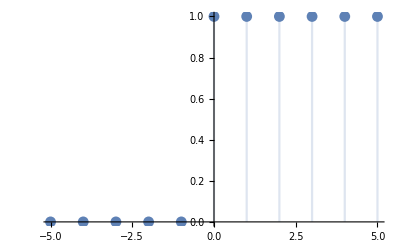

```mathematica
DiscretePlot[UnitStep[2k],{k,-5,5}]
```